Номер 4
Условие:
Используя таблицу значений функции f(x) в равноотстоящих точках
отрезка [0, 6], полученной в задании 1 при n = 10, выполнить следующие действия:
а) построить интерполяционный кубический сплайн дефекта 1 S_3(x) для функции f(x), проиллюстрировать графически (изобразить точки (x_i, f(x_i)) и графики функций f(x) и S_3(x) на одном чертеже);
б) выполнить интерполяцию сплайном Sf(x) с помощью функции
Interpolation[data, Method->“Spline”], проиллюстрировать графически;
в) построить интерполяционный кубический сплайн Spl с помощью
функции SplineFit[data, Cubic] (предварительно загрузить пакет сплайн-интерполяции командой Needs[“Splines`”]), проиллюстрировать графически (для построения графика сплайна Spl использовать функцию ParametricPlot);
г) вычислить значения функции f(x) и построенных интерполяционных
сплайнов S_3(x), Sf(x) иSpl в точке x = 2,4316.

Функция f(x):

```mathematica
f[x_]=3+(2/7 x-Cosh[(3x)/13]) Log[x^2+2 x+3]
```

Значения из условия задания и шаг интерполяции h для равноотстоящих узлов:

```mathematica
a=0;b=6;n=10;x0=2.4316;h=(b-a)/n;
```

График функции f(x):

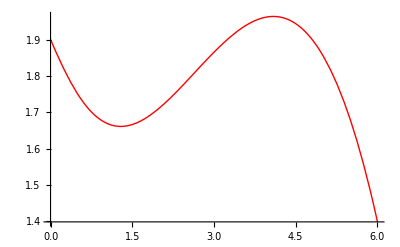

```mathematica
graph=Plot[f[x],{x,a,b},PlotStyle->{Red,Thick}]
```

Возьмём таблицу значений функции для равноотстоящих узлов (h_i = h) на промежутке для n = 10:

```mathematica
data=Table[{i h,f[i h]},{i,0,n}]//N;
```

```mathematica
TableForm[data]
```

0. | 1.90139
0.6 | 1.72822
1.2 | 1.66226
1.8 | 1.68933
2.4 | 1.77043
3. | 1.86632
3.6 | 1.94154
4.2 | 1.96364
4.8 | 1.90147
5.4 | 1.72369
6. | 1.39751

Для получения кубического сплайна дефекта 1 найдём коэффициенты c_k с помощью встроенной функции LinearSolve.

```mathematica
listC=Table[0,{i,0,n}];
```

```mathematica
A=Table[0,{n-1},{n-1}];
```

```mathematica
Do[If[i≠1,A[[i,i-1]]=h];A[[i,i]]=4 h;If[i≠n-1,A[[i,i+1]]=h],{i,1,n-1}]
```

```mathematica
A//MatrixForm//N
```

(2.4 | 0.6 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.6 | 2.4 | 0.6 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.6 | 2.4 | 0.6 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.6 | 2.4 | 0.6 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.6 | 2.4 | 0.6 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.6 | 2.4 | 0.6 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.6 | 2.4 | 0.6 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.6 | 2.4 | 0.6
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.6 | 2.4)

Столбец свободных членов:

```mathematica
B=Table[3 ((data[[i,2]]-data[[i-1,2]])/h-(data[[i-1,2]]-data[[i-2,2]])/h),{i,3,n+1}]//N;
```

```mathematica
X=LinearSolve[A,B];
```

```mathematica
For[i=1,i≤n-1,i++,listC[[i+1]]=X[[i]]];
```

```mathematica
MatrixForm[listC]
```

(0
0.191604
0.126913
0.0760454
0.0191902
-0.0296279
-0.0728128
-0.121883
-0.141938
-0.273696
0)

Зададим остальные коэффициенты кубического сплайна:

```mathematica
listA=Table[data[[i+1,2]],{i,1,n}]
```

{1.72822,1.66226,1.68933,1.77043,1.86632,1.94154,1.96364,1.90147,1.72369,1.39751}

```mathematica
listB=Table[(data[[i,2]]-data[[i-1,2]])/h+2/3 h listC[[i]]+1/3 h listC[[i-1]],{i,2,n+1}]
```

{-0.211968,-0.0208576,0.100917,0.158059,0.151796,0.0903318,-0.0264858,-0.184778,-0.434159,-0.598377}

```mathematica
listD=Table[(listC[[i]]-listC[[i-1]])/(3 h),{i,2,n+1}]
```

{0.106447,-0.0359397,-0.0282598,-0.0315862,-0.0271212,-0.0239916,-0.0272613,-0.0111414,-0.0731994,0.152054}

Теперь зададим кубический сплайн в виде кусочно заданной функции:

```mathematica
sData=Table[{listA[[i]]+listB[[i]] (x-data[[i+1,1]])+listC[[i+1]] (x-data[[i+1,1]])^2+listD[[i]] (x-data[[i+1,1]])^3,data[[i,1]]≤x≤data[[i+1,1]]}, {i,1,n}]//Simplify
```

```mathematica
S[x_]=Piecewise[sData]
```

Piecewise[{{1.90139-0.326931 x+2.77556×10^-17 x^2+0.106447 x^3, 0.≤x≤0.6}, {1.93214-0.480708 x+0.256296 x^2-0.0359397 x^3, 0.6≤x≤1.2}, {1.91887-0.447531 x+0.228648 x^2-0.0282598 x^3, 1.2≤x≤1.8}, {1.93827-0.479864 x+0.246611 x^2-0.0315862 x^3, 1.8≤x≤2.4}, {1.87655-0.402708 x+0.214463 x^2-0.0271212 x^3, 2.4≤x≤3.}, {1.79205-0.318209 x+0.186296 x^2-0.0239916 x^3, 3.≤x≤3.6}, {1.9446-0.445337 x+0.22161 x^2-0.0272613 x^3, 3.6≤x≤4.2}, {0.750306+0.407731 x+0.0184982 x^2-0.0111414 x^3, 4.2≤x≤4.8}, {7.61342-3.88172 x+0.912133 x^2-0.0731994 x^3, 4.8≤x≤5.4}, {-27.8558+15.8234 x-2.73696 x^2+0.152054 x^3, 5.4≤x≤6.}, {0, True}}]

Изобразим полученный кубический сплайн.

```mathematica
graphD=ListPlot[data,PlotStyle->{Darker,PointSize[0.02]}];
```

```mathematica
graphS=Plot[S[x],{x,a,b}];
```

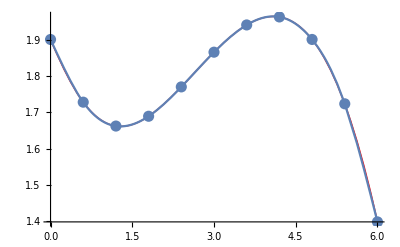

```mathematica
Show[graph,graphD,graphS]
```

б)

Интерполируем функцию сплайном с помощью функции Interpolation:

```mathematica
Sf[x_]=Interpolation[data,x,Method->"Spline"]
```

InterpolatingFunction[…][x]

Изобразим полученный сплайн.

```mathematica
graphSf=Plot[Sf[x],{x,a,b}];
```

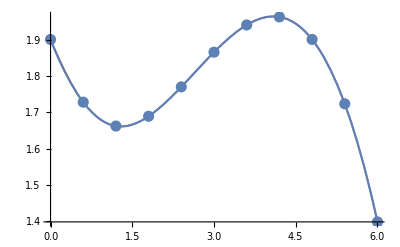

```mathematica
Show[graph,graphD,graphSf]
```

в)

Получим интерполяционный кубический сплайн с помощью функции SplineFit:

```mathematica
Needs["Splines`"]
```

```mathematica
Spl=SplineFit[data,Cubic]
```

SplineFunction[Cubic, {0.,10.}, <>]

Изобразим полученный сплайн.

```mathematica
t=(x-a)/h;
```

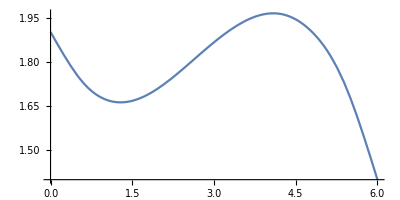

```mathematica
graphSpl=ParametricPlot[Spl[t],{t,0,n},AspectRatio->1/2]
```

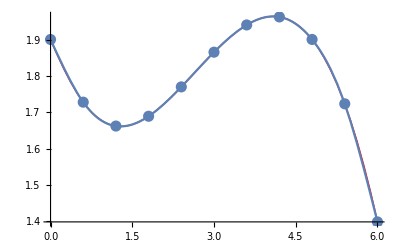

```mathematica
Show[graph,graphD,graphSpl]
```

г)

Значение интерполяционного кубического сплайна в точке x0:

```mathematica
Print["S[x0]=",S[x0]]
```

S[x0]=1.77544

Значение интерполирующей функции-сплайна в точке x0:

```mathematica
Print["Sf[x0]=",Sf[x0]]
```

Sf[x0]=1.77543

Значение интерполяционного кубического сплайна, построенного с помощью SplineFit, в точке x0:

```mathematica
Print["Spl[x0]=",Last[Spl[(x0-a)/h]]]
```

Spl[x0]=1.77544